## Solution CP-10: Graphical analysis of non-linear systems

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Graphical analysis of non-linear systems

For an overview of the relevant Mathematica commands, refer to chapter 12 of the tutorial, and also to chapters 9 & 10, since many commands are very similar to those used in linear systems (e.g., how to plot time and phase diagrams).

### Exercise 10-1: Morley’s catastrophe

For this exercise we analyze a functional response curve of Holling type III: ⅆN/ⅆt=r·N·(1-N/K)-P·E·N^2/(N^2+H^2)

(a) Make a time-plot for parameters r=1, K=10, E=5, H=0.5, P=0.1 and N_0=10

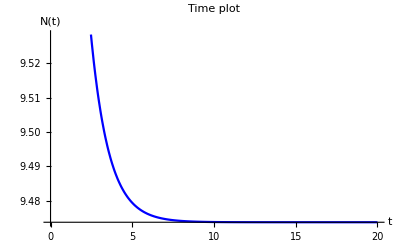

```mathematica
r=1;
k=10;
e=5;
h=0.5;
eq=D[n[t],t]==r*n[t]*(1-n[t]/k)-p*e*n[t]^2/(n[t]^2+h^2);
sol=NDSolveValue[{eq/.p->0.1,n[0]==10},n[t],{t,0,20}];
Plot[sol,{t,0,20},PlotLabel->"Time plot",AxesLabel->{"t","N(t)"},PlotStyle->{Blue}]
```

(b) Increase P from 0.1 to 0.6 in steps of 0.1, and find the equilibrium N̂ where the system collapses.

```mathematica
timePlot1[p_,n0_]:=Module[{t,sol},
eq=D[n[t],t]==r*n[t]*(1-n[t]/k)-p*e*n[t]^2/(n[t]^2+h^2);
sol=NDSolveValue[{eq,n[0]==n0},n[t],{t,0,20}];
Plot[sol,{t,0,20},PlotRange->{0,10}, PlotLabel->"Time plot",AxesLabel->{"t","N(t)"},PlotStyle->{Blue}]
]
```

```mathematica
Manipulate[timePlot1[p,n0],{p,0.1,0.6,0.1},{n0,10}]
```

Between P = 0.5 and P = 0.6 the system collapses.
(c) Set N_0=N̂ , and decrease P from 0.6 to 0.1 in steps of 0.1. At which point will the system recover?

```mathematica
Manipulate[timePlot1[p,n0],{p,0.6,0.1,-0.1},{n0,0.085}]
```

Between P = 0.2 and 0.1 we see that the system recovers. So the system collapsed when P was between 0.5 and 0.6. Reducing P to 0.5 does not make the system recover; a reduction all the way down to 0.1 is necessary for this. This is called a hysteresis effect.
(d) Plot ⅆN/ⅆt against N for P=0.1, 0.3 and 0.6. How many equilibria do you find?

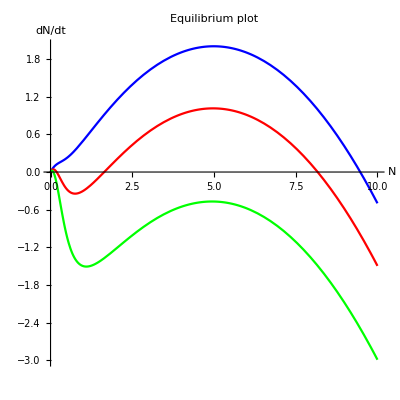

```mathematica
f=r*n*(1-n/k)-p*e*n^2/(n^2+h^2);
fP1=f/.p->0.1;
fP3=f/.p->0.3;
fP5=f/.p->0.6;
Plot[{fP1,fP3,fP5},{n,0,10},PlotLabel->"Equilibrium plot",AspectRatio->1,AxesLabel->{"N","dN/dt"},PlotStyle->{Blue,Red,Green}]
```

We observe that the function has a different number of intersections with the N-axis for different values of P.Hence, the number of equilibria depends on P.Again we see that when we increase P (from  blue to green), the only stable equilibrium is initially a high prey density (blue), which decreases slowly when P increases, but suddenly disappears when the high- density intersection disappears.

```mathematica
equil1=Values[NSolve[{fP1==0},{n},Reals]]
equil3=Values[NSolve[{fP3==0},{n},Reals]]
equil5=Values[NSolve[{fP5==0},{n},Reals]]
```

{{0.},{9.47369}}

{{0.},{0.18626},{1.64263},{8.17111}}

{{0.},{0.0850135}}

We see that the number of equilibria indeed changes as we change P.
(e) Make a “catastrophe diagram” by plotting N̂ against P.

0.34

0.431667

0.180556

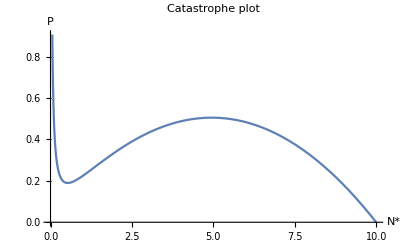

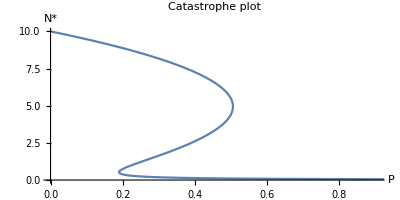

```mathematica
f=r*n*(1-n/k)-p*e*n^2/(n^2+h^2);
equi[m_]:=Values[Solve[f==0/.{n->m},p]//First//First]
equi[2]
equi[3]
equi[9]
Plot[equi[n],{n,0,10},PlotLabel->"Catastrophe plot",AxesLabel->{"N*","P"}]
ParametricPlot[{equi[n],n},{n,0.01,10},AspectRatio-> 1/2,PlotRange->Automatic,PlotLabel->"Catastrophe plot",AxesLabel->{"P","N*"}]
```

The part of this graph that lies between the upper and the lower equilibrium is an unstable equilibrium and is called a separatrix. It separates the regions of the stable equilibria. If we start with a population size below this separatrix we will end up in the lower equilibrium and if we start in a higher population size, then we will end up in the higher equilibrium. This diagram also shows the catastrophe. If we have a low P there is only one, high-density, equilibrium for N. As we increase P, the unstable equilibrium appears around P = 0.2. The system remains in the high equilibrium but when P is increased further, then around P = 0.52, the system collapses to the low equilibrium close to zero. If we then bring back P to lower values we have to go all the way down to values below P = 0.2, to regain the high-density equilibrium.

### Exercise 10-2: The Rosenzweig-McArthur model

For this exercise we consider the Rosenzweig-McArthur model with type III functional response: ⅆR/ⅆt=r·R·(1-R/K)-(b·R^2N)/(h^2+R^2), ⅆN/ⅆt=(c·b·N·R^2)/(h^2+R^2)-d·N, with parameters r=1, b=1,c=4, h=16.

(a) Draw the time plots for various values of d (between 1 and 3.99) and K (between 1 and 500).

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

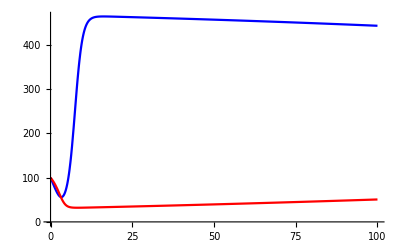

```mathematica
r=1;
b=1;
c=4;
h=16;
eq1=D[R[t],t]==r*R[t]*(1-R[t]/KK)-b*R[t]^2*NN[t]/(h^2+R[t]^2);
eq2=D[NN[t],t]==c*b*R[t]^2*NN[t]/(h^2+R[t]^2)-d*NN[t];
init={R[0]==100,NN[0]==100};
sol1=NDSolveValue[{eq1,eq2,init},{R[t],NN[t]},{t,0,100}]/.{d->3.99,KK->500};
Plot[sol1,{t,0,100},PlotStyle->{Blue,Red}]
```

```mathematica
timePlot2[d0_,K0_]:=Module[{t,sol},
eq1=D[R[t],t]==r*R[t]*(1-R[t]/K0)-b*R[t]^2*NN[t]/(h^2+R[t]^2);
     eq2=D[NN[t],t]==c*b*R[t]^2*NN[t]/(h^2+R[t]^2)-d0*NN[t];
     init={R[0]==100,NN[0]==100};
sol=NDSolveValue[{eq1,eq2,init},{R[t],NN[t]},{t,0,100}];
Plot[sol,{t,0,100},PlotRange->All, PlotStyle->{Blue,Red}]
]
```

```mathematica
Manipulate[timePlot2[d0,K0],{d0,1.,3.99},{K0,1,500}]
```

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t$3089 == 0..

NDSolveValue::dsvar: 0.00204286 cannot be used as a variable.

NDSolveValue::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

In most cases we see a stable equilibrium point, sometimes with damped oscillations. For certain settings of d0 and K0 we find limit cycles, periodic oscillating behavior.

(b) Now assume K=130. Draw the null clines in a phase plane plot and look how the null clines change for different values of d.

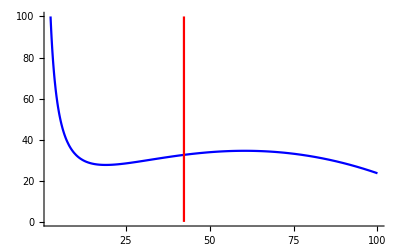

```mathematica
eq3=r*R[t]*(1-R[t]/KK)-b*R[t]^2*NN[t]/(h^2+R[t]^2)==0;
eq4=c*b*R[t]^2*NN[t]/(h^2+R[t]^2)-d*NN[t]==0;
sol3=Values[Solve[eq3,NN[t]]];
sol4=Values[Solve[eq4,R[t]]];
vsol1=Flatten[sol3/.R[t]->RR];
vsol2=Flatten[sol4/.R[t]->RR];
p1=Plot[vsol1/.KK->130,{RR,0,100},PlotStyle->Blue, PlotRange->{{0,100},{0,100}}];
p2=ParametricPlot[{vsol2[[2]]/.{d->3.5,KK->130},t},{t,0,100},PlotStyle->Red];
Show[{p1,p2},PlotRange->All]
```

```mathematica
phasePlanePlot[d0_,K0_]:=Module[{p1,p2},
p1=Plot[vsol1/.KK->K0,{RR,0,200},PlotStyle->Blue, PlotRange->{{0,200},{0,100}}];
p2=ParametricPlot[{vsol2[[2]]/.{d->d0,KK->K0},t},{t,0,100},PlotStyle->Red];
Show[{p1,p2},PlotRange->All]
]
```

```mathematica
Manipulate[phasePlanePlot[d0,K0],{d0,1,3.99},{K0,1,500}]
```

For low values of K0, the blue nullcline is monotonically decreasing. When K0 is high enough, the blue curve has a intermediate minimum and maximum. When the equilibrium lies between them, we have limit cycles. 

(c) Determine the stability of the intersection point of the two null clines (i.e., the equilibrium) for the different values of d.

```mathematica
s1=r*R*(1-R/KK)-b*R^2*NN/(h^2+R^2);
s2=c*b*R^2*NN/(h^2+R^2)-d*NN;
sol2=Values[NSolve[{s1==0,s2==0},{NN,R}]]/.{KK->130,d->3.}
```

{{0.,0.},{-44.8273,-27.7128},{29.0735,27.7128},{0,130}}

```mathematica
jac=D[{s1,s2},{{NN,R}}]/.{KK->130,d->3.}
```

{{-R^2/(256+R^2),1-R/65+(2 NN R^3)/((256+R^2)^2)-(2 NN R)/(256+R^2)},{-3.+(4 R^2)/(256+R^2),-(8 NN R^3)/((256+R^2)^2)+(8 NN R)/(256+R^2)}}

```mathematica
jac1=jac/.{NN->sol2[[1,1]],R->sol2[[1,2]]};
Eigenvalues[jac1]
```

{0.+1.73205 ⅈ,0.-1.73205 ⅈ}

```mathematica
jac2=jac/.{NN->sol2[[2,1]],R->sol2[[2,2]]};
Eigenvalues[jac2]
```

{2.42635,-0.75}

```mathematica
jac3=jac/.{NN->sol2[[3,1]],R->sol2[[3,2]]};
Eigenvalues[jac3]
```

{1.57365,-0.75}

```mathematica
jac4=jac/.{NN->sol2[[4,1]],R->sol2[[4,2]]};
Eigenvalues[jac4]
```

{-0.492539+0.835295 ⅈ,-0.492539-0.835295 ⅈ}

For these examples only the last equilibrium is stable, with damped oscillations.

(d) Draw the solution of the system of ODEs from (a) in the phase plane plot and look at how it changes as d  changes from 1 to 3.99.

```mathematica
limitCyclePlot[d0_,K0_]:=Module[{t,sol,eq1,eq2,init,s1,s2},
eq1=D[R[t],t]==r*R[t]*(1-R[t]/K0)-b*R[t]^2*NN[t]/(h^2+R[t]^2);
     eq2=D[NN[t],t]==c*b*R[t]^2*NN[t]/(h^2+R[t]^2)-d0*NN[t];
     init={R[0]==100,NN[0]==100};
sol=NDSolveValue[{eq1,eq2,init},{R[t],NN[t]},{t,0,100}];
s1=r*R*(1-R/K0)-b*R^2*NN/(h^2+R^2);
     s2=c*b*R^2*NN/(h^2+R^2)-d0*NN;
p4=ParametricPlot[sol,{t,0,100},PlotRange->{{0,120},{0,300}},PlotStyle->Green];
p5=Plot[vsol1/.KK->K0,{RR,0,120},PlotRange->{{0,120},{0,300}},PlotStyle->Blue];
p6=ParametricPlot[{vsol2[[2]]/.{d->d0,KK->K0},t},{t,0,300},PlotStyle->Red];
p7=StreamPlot [{s1,s2},{R,0,120},{NN,0,300},StreamScale->{Tiny,Automatic,0.01}, StreamStyle->Pink];
Show[{p4,p5,p6,p7},AspectRatio->1,AxesLabel->{"R","N"}]
]
```

```mathematica
Manipulate[limitCyclePlot[d0,K0],{d0,1,3.99},{K0,130}]
```

The green line is a single trajectory in time. This figure shows beautifully the limit cycles around the interactions of the null clines when K0 is large enough and d0 is in a a certain region. As K0 increases the oscillations can get larger and N or R can get close to 0, and in a natural system it would be expected that stochasticity will lead to extinction. Hence, enriching the system by increasing K0, will lead to collapse rather than higher densities, i.e. the paradox of enrichment.